```mathematica
Consider Gierer-Meinhardt reaction-diffusion equations:
```

Define the reaction functions

```mathematica
f[u_,v_]=a*u^2/v+k-α*u
g[u_,v_]=a*u^2-β*v
```

k+(a u^2)/v-u α

a u^2-v β

```mathematica
{{us,vs}}={u,v}/.Solve[{f[u,v]==0,g[u,v]==0},{u,v}]
```

{{(k+β)/α,(a (k+β)^2)/(α^2 β)}}

```mathematica
fu=D[f[u,v],u]/.{u->us,v->vs}//FullSimplify
```

α-(2 k α)/(k+β)

```mathematica
fv=D[f[u,v],v]/.{u->us,v->vs}//Simplify
```

-(α^2 β^2)/(a (k+β)^2)

```mathematica
gu=D[g[u,v],u]/.{u->us,v->vs}//Simplify
```

(2 a (k+β))/α

```mathematica
gv=D[g[u,v],v]/.{u->us,v->vs}//Simplify
```

-β

```mathematica
detA=fu*gv-fv*gu//FullSimplify
```

α β

Next determine the range of a,b that are possible for the Turing instability.

```mathematica
trA=(fu+gv)//FullSimplify
```

α-β-(2 k α)/(k+β)

```mathematica
R1[α_,β_,k_]= trA
```

α-β-(2 k α)/(k+β)

```mathematica
Solve[{{R1[α,β,k]/.{k->0.5}}==0,α*β>0},β]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{β→ConditionalExpression[0.25 (-1.+2. α)-0.25 √(1.-12. α+4. α^2), α>2.91421||α<0]},{β→ConditionalExpression[0.25 (-1.+2. α)+0.25 √(1.-12. α+4. α^2), α>2.91421]}}

```mathematica
(*the full condition is in the notes for HW4*)
```

```mathematica
Range of unstable wavenumbers
Recall that m=π l^2
```

```mathematica
of Range unstable wavenumbers
```

of Range unstable wavenumbers

```mathematica
l^2
```

l^2

```mathematica
h[m_]=m^2-g*(fu+gv)*m+g^2*detA//FullSimplify
```

m^2+g^2 α β+g m (β+(α (k-β))/(k+β))

```mathematica
Max growing mode
```

```mathematica
mMax=m/.Solve[D[h[m],m]==0,m]
```

{-(g (k α+k β-α β+β^2))/(2 (k+β))}

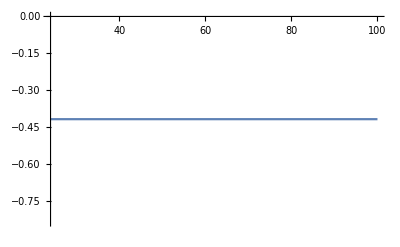

```mathematica
Plot[mMax/.{g->10,α->3,β->1.75,k->0.5},{d,24,100}]
```

```mathematica
mmMax=mMax/.{α->3,β->1.75,k->0}
```

{0.625 g}

```mathematica
(* So, the fastest growing mode, when g=10, is given by *)
l=Sqrt[0.625*g]/Pi/.{g->100}
```

2.51646

```mathematica
(* 

This means that no modes will grow in the simulation since l≥1 in practice. Next, let's choose g to make a specific mode the maximum growing mode.

*)
```

```mathematica
gmax[lmax_]=(Pi*lmax)^2/.625
```

15.7914 lmax^2

```mathematica
gmax[3]
```

142.122

```mathematica
Consider the Gierer-Meinhardt reaction-diffusion equations:


Let u be the activator and v be the inhibitor.

(∂u(x,t))/(∂t) = D(∂^2 u(x,t))/(∂x^2)+(au^2/v+U-αu)

(∂v(x,t))/(∂t) =d D (∂^2 v(x,t))/(∂x^2)+(au^2-βv)
```

```mathematica
Define the parameters appearing in system, which is instable
```

```mathematica
α=3;
β=1.75;
a=1;
k=0.5;
h=0.0;
DD=1;
```

```mathematica
{{ustar,vstar}}={u,v}/.Solve[{f[u,v]==0,g[u,v]==0},{u,v}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{0.75,0.321429}}

```mathematica
{ub,vb}=0*{ustar,vstar}
```

{0.,0.}

```mathematica
kb=0;
l1=2;
l2=3;
l3=4;
l4=7;
l5=8;
a1=1;
a2=0;
a3=0;
a4=1;
a5=1;
```

```mathematica
{usol,vsol} = {u,v}/.NDSolve[{
D[u[t,x], t] == a*u[t,x]*u[t,x]/ v[t,x]+k-α*u[t,x]+DD*D[u[t,x],{x,2}],
D[v[t,x], t] == a*u[t,x]*u[t,x]-β*v[t,x]+ DD*D[v[t,x],{x,2}],  
(D[u[t,x],x]/.x->0)==kb(u[t,0]-ub),
(D[u[t,x],x]/.x->1)==-kb(u[t,1]-ub),
(D[v[t,x],x]/.x->0)==kb(v[t,0]-vb),
(D[v[t,x],x]/.x->1)==-kb(v[t,1]-vb),
u[0,x] ==2+.25*(a1*Cos[l1*Pi*x]^2+a2*Cos[l2*Pi*x]+a3*Cos[l3*Pi*x]+a4*Cos[l4*Pi*x]+a5*Cos[l5*Pi*x]),
v[0,x] ==0.5-.25*(a1*Cos[l1*Pi*x]+a2*Cos[l2*Pi*x]+a3*Cos[l3*Pi*x]+a4*Cos[l4*Pi*x]+a5*Cos[l5*Pi*x])
}, 
{u,v}, 
{t,0,40},
{x,0,1},
Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->1800}},
PrecisionGoal->3
][[1]];
```

```mathematica
Manipulate[Plot[{usol[t,x],vsol[t,x]},{x,0,1},PlotRange->{{0,1},{0,8}},PlotLabels->{"u","v","Cos[6*Pi*x]"}],{t,0,35,.005}]
```

```mathematica
Define the parameters appearing in system,which is stable
```

```mathematica
α=3;
β=4;
a=1;
k=0.5;
h=0.0;
DD=1;
```

```mathematica
kb=0;
l1=2;
l2=3;
l3=4;
l4=7;
l5=8;
a1=0;
a2=0;
a3=1;
a4=1;
a5=1;
{{ustar,vstar}}={u,v}/.Solve[{f[u,v]==0,g[u,v]==0},{u,v}]
{ub,vb}=0*{ustar,vstar}
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{1.5,0.5625}}

{0.,0.}

```mathematica
{usol,vsol} = {u,v}/.NDSolve[{
D[u[t,x], t] == a*u[t,x]*u[t,x]/ v[t,x]+k-α*u[t,x]+DD*D[u[t,x],{x,2}],
D[v[t,x], t] == a*u[t,x]*u[t,x]-β*v[t,x]+ DD*D[v[t,x],{x,2}],  
(D[u[t,x],x]/.x->0)==kb(u[t,0]-ub),
(D[u[t,x],x]/.x->1)==-kb(u[t,1]-ub),
(D[v[t,x],x]/.x->0)==kb(v[t,0]-vb),
(D[v[t,x],x]/.x->1)==-kb(v[t,1]-vb),
u[0,x] ==2+.25*(a1*Cos[l1*Pi*x]^2+a2*Cos[l2*Pi*x]+a3*Cos[l3*Pi*x]+a4*Cos[l4*Pi*x]+a5*Cos[l5*Pi*x]),
v[0,x] ==0.5-.25*(a1*Cos[l1*Pi*x]+a2*Cos[l2*Pi*x]+a3*Cos[l3*Pi*x]+a4*Cos[l4*Pi*x]+a5*Cos[l5*Pi*x])
}, 
{u,v}, 
{t,0,40},
{x,0,1},
Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->1800}},
PrecisionGoal->3
][[1]];
```

```mathematica
Manipulate[Plot[{usol[t,x],vsol[t,x]},{x,0,1},PlotRange->{{0,1},{0,8}},PlotLabels->{"u","v","Cos[6*Pi*x]"}],{t,0,35,.005}]
```

```mathematica
The difference between stable parameter and unstable parameter is that the stable parameter will oscilated converge to one constant line and stay there.  But the unstbale parameter will cause the u and v oscilation to each other around the answer.
```